```mathematica
$Assumptions={Subscript[m,b]>0,Subscript[τ,s]>0,Subscript[r, b]>0,α >0, β > 0}
```

{m_b>0,τ_s>0,r_b>0,α>0,β>0}

```mathematica
ToExpression["\\rho \\left(\\frac{3\\sqrt{\\pi}m_b}{4\\rho}\\right)^{\\frac23}\\left( 1 + \\sqrt{\\frac{\\tau_s}{\\tau_b}} \\right)^2 c_s g(\\tau_b - \\tau_s)",TeXForm]
```

1/2 3^(2/3) (π/2)^(1/3) ρ g[τ_b-τ_s] c_s (m_b/ρ)^(2/3) (1+√(τ_s/τ_b))^2

```mathematica
expr =  (Subscript[τ, b]-Subscript[τ, s]) (Subscript[m, b])^(2/3) (1+√(Subscript[τ, s]/Subscript[τ, b]))^2/.{Subscript[τ, b]-> α Subscript[r, b]^2,Subscript[m, b]->β Subscript[r, b]^3 }//FullSimplify
```

(β r_b^3)^(2/3) (α r_b^2-τ_s) (1+√(τ_s/(α r_b^2)))^2

```mathematica
Ans = 2/(Subscript[c, s] ρ^(1/3) g   3^(2/3) (π/2)^(1/3))Integrate[3β Subscript[r, b]^2/expr, Subscript[r, b]]
```

((3/π)^(1/3) β^(1/3) (-ArcTanh[(√α r_b)/(√τ_s)]/(√α √τ_s)+(2 τ_s (-r_b+√(τ_s/α)))/((-α r_b^2+τ_s)^2)+(-3 r_b+4 √(τ_s/α))/(α r_b^2-τ_s)))/(2^(2/3) g ρ^(1/3) c_s)

```mathematica
Ans = Ans/.{β -> 4π ρ/3, α -> 2ρ/(9ν),Subscript[r, b]-> Subscript[d, b]/2,Subscript[τ, s]-> 1/(18ν)Subscript[d, s]^2 ρ}//FullSimplify
```

-(9 ν (3 d_b^3 d_s-d_b d_s^3-4 d_b^2 d_s √(d_s^2)+2 d_s^3 √(d_s^2)+ArcTanh[d_b/d_s] (d_b^2-d_s^2)^2))/(g ρ c_s d_s (d_b^2-d_s^2)^2)

```mathematica
Ans0 = Ans/.{Subscript[d, b]->Subscript[d, b0]}//FullSimplify
```

-(9 ν (3 d_b0^3 d_s-d_b0 d_s^3-4 d_b0^2 d_s √(d_s^2)+2 d_s^3 √(d_s^2)+ArcTanh[d_b0/d_s] (d_b0^2-d_s^2)^2))/(g ρ c_s d_s (d_b0^2-d_s^2)^2)

```mathematica
expr2  = Ans -Ans0 //FullSimplify
```

(9 ν ((-3 d_b^3 d_s+d_b d_s^3+4 d_b^2 d_s √(d_s^2)-2 d_s^3 √(d_s^2)-ArcTanh[d_b/d_s] (d_b^2-d_s^2)^2)/((d_b^2-d_s^2)^2)+(3 d_b0^3 d_s-d_b0 d_s^3-4 d_b0^2 d_s √(d_s^2)+2 d_s^3 √(d_s^2)+ArcTanh[d_b0/d_s] (d_b0^2-d_s^2)^2)/((d_b0^2-d_s^2)^2)))/(g ρ c_s d_s)

```mathematica
G[x_]:=(3 x+2)/(1+x)^2+ArcTanh[x];

new=3/(Sqrt[2] g Subscript[c,s]) Sqrt[ν/(ρ Subscript[τ,s])]*(G[Sqrt[Subscript[τ,b0]/Subscript[τ,s]]]-G[Sqrt[Subscript[τ,b]/Subscript[τ,s]]])
```

(3 (-ArcTanh[√(τ_b/τ_s)]+ArcTanh[√(τ_b0/τ_s)]-(2+3 √(τ_b/τ_s))/(1+√(τ_b/τ_s))^2+(2+3 √(τ_b0/τ_s))/(1+√(τ_b0/τ_s))^2) √(ν/(ρ τ_s)))/(√2 g c_s)

```mathematica
FullSimplify[expr2 - new/.{Subscript[τ, b]-> 1/(18ν)Subscript[d, b]^2 ρ,Subscript[τ, s]-> 1/(18ν)Subscript[d, s]^2 ρ,Subscript[τ, b0]-> 1/(18ν)Subscript[d, b0]^2 ρ} ,Subscript[d,b]>0&&Subscript[d,b0]>0&&Subscript[d,s]>0&&ν>0&&ρ>0]
```

0

```mathematica
FullSimplify[new /.{Subscript[τ, b]-> 1/(18ν)Subscript[d, b]^2 ρ,Subscript[τ, s]-> 1/(18ν)Subscript[d, s]^2 ρ,Subscript[τ, b0]-> 1/(18ν)Subscript[d, b0]^2 ρ},Subscript[d,b]>0&&Subscript[d,b0]>0&&Subscript[d,s]>0&&ν>0&&ρ>0]
```

(9 ν (-ArcTanh[d_b/d_s]+ArcTanh[d_b0/d_s]-(d_s (3 d_b+2 d_s))/(d_b+d_s)^2+(d_s (3 d_b0+2 d_s))/(d_b0+d_s)^2))/(g ρ c_s d_s)

```mathematica
(9 ν (-ArcTanh[Subscript[d, b]/Subscript[d, s]]+ArcTanh[Subscript[d, b0]/Subscript[d, s]]-(Subscript[d, s] (3 Subscript[d, b]+2 Subscript[d, s]))/(Subscript[d, b]+Subscript[d, s])^2+(Subscript[d, s] (3 Subscript[d, b0]+2 Subscript[d, s]))/(Subscript[d, b0]+Subscript[d, s])^2))/(g ρ Subscript[c, s] Subscript[d, s])/.{Subscript[d, b0]-> Subscript[d, b]/d,Subscript[d, s]-> Subscript[d, b]/Subscript[d, r]}//FullSimplify
```

(9 ν d_r (-ArcTanh[d_r]+ArcTanh[d_r/d]+(-2-3 d_r)/(1+d_r)^2+(d (2 d+3 d_r))/(d+d_r)^2))/(g ρ c_s d_b)

```mathematica
toplot = (9 ν Subscript[d, r] (-ArcTanh[Subscript[d, r]]+ArcTanh[Subscript[d, r]/d]+(-2-3 Subscript[d, r])/(1+Subscript[d, r])^2+(d (2 d+3 Subscript[d, r]))/(d+Subscript[d, r])^2))/(g ρ Subscript[c, s] Subscript[d, b])/.{g->9.81,Subscript[c, s]-> 10^-7,ρ -> 1000, Subscript[d, b]-> 10^-5,Subscript[d, r]-> 2.7*10^-6,ν -> 10^-5}
```

0.0247706 (-2.+(d (8.1×10^-6+2 d))/((2.7×10^-6+d)^2)+ArcTanh[(2.7×10^-6)/d])

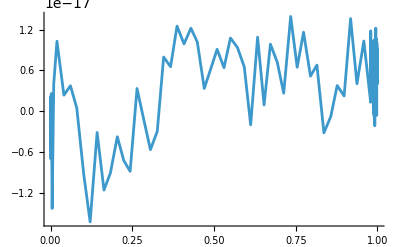

```mathematica
Plot[toplot,{d,1,100000000}]
```